```mathematica
block[sys_,xb_Integer,yb_Integer]:=sys[[1+(xb-1)*3;;xb*3,1+(yb-1)*3;;yb*3]];
blockf[sys_,xb_Integer,yb_Integer]:=Flatten[block[sys,xb,yb],1];
blockcoords[x_Integer,y_Integer]:={Quotient[x-1,3]+1,Quotient[y-1,3]+1};
blockofelem[sys_,x_Integer,y_Integer]:=Block[{xb=Quotient[x-1,3],yb=Quotient[y-1,3]},Return[block[sys,xb+1,yb+1]]];
blockofelemf[sys_,x_Integer,y_Integer]:=Flatten[blockofelem[sys,x,y],1];
getdiff[ls_]:=Complement[Range[9],ls];
calcp[sys_,x_Integer,y_Integer]:=
(
Module[{res,t1,t2,t3},
res={};
(*Print["elem = ",sys[[x,y]]]*)
If[sys[[x,y]]==0,
(* Check row *)
t1=getdiff[sys[[x]]];
(* Check col *)
t2=getdiff[sys[[;;,y]]];
(* Check block *)
t3=getdiff[blockofelemf[sys,x,y]];
res=Intersection[t1,t2,t3];
];
Return[res];
];
)
calcpall[sys_]:=Map[calcp[sys,#[[1]],#[[2]]]&,Table[{x,y},{x,9},{y,9}],{2}];
sudokugrid={Directive[Thick,Black],Line[{{{0,0},{0,9}},{{3,0},{3,9}},{{6,0},{6,9}},{{9,0},{9,9}}}],Line[{{{0,0},{9,0}},{{0,3},{9,3}},{{0,6},{9,6}},{{0,9},{9,9}}}],Directive[Dashed,Blue,Thin],Line[{{{1,0},{1,9}},{{2,0},{2,9}},{{4,0},{4,9}},{{5,0},{5,9}},{{7,0},{7,9}},{{8,0},{8,9}}}],Line[{{{0,1},{9,1}},{{0,2},{9,2}},{{0,4},{9,4}},{{0,5},{9,5}},{{0,7},{9,7}},{{0,8},{9,8}}}]};
gc[i_Integer,j_Integer]:={j-1,9-i+1};
gcelem[elem_Integer]:=Switch[elem,1,{1/6,-1/6},2,{3/6,-1/6},3,{5/6,-1/6},4,{1/6,-3/6},5,{3/6,-3/6},6,{5/6,-3/6},7,{1/6,-5/6},8,{3/6,-5/6},9,{5/6,-5/6}];
fills[s_,colour_:Black]:=Block[{ls={},i,j},For[i=1,i≤9,++i,For[j=1,j≤9,++j,If[s[[i,j]]≠0,ls=Append[ls,Text[Style[ToString[#],Bold,Large,colour]&@s[[i,j]],gc[i,j]+{0.5,-0.5}]]];]];Return[ls]];
putpelem[i_Integer,j_Integer,elem_Integer,colour_:Black]:=Text[Style[ToString[elem],colour,Bold],gc[i,j]+gcelem[elem]];
fillp[p_,colour_:Red]:=Block[{ls={},i,j},For[i=1,i≤9,++i,For[j=1,j≤9,++j,If[Length[p[[i,j]]]>0,ls=Join[ls,(putpelem[i,j,#,colour]&/@p[[i,j]])];];]];Return[ls]];
displaysys[systate_,sysp_,opts_:{}]:=Graphics[Join[sudokugrid,fills[systate],fillp[sysp],opts]];
gridtitle[str_String]:=Text[Style[ToString[str],Black,Bold,Large],{4.5,9.5},Center];
findmove[sys_,sysp_]:=
(
Module[{res,i,j,title,melems,eelems},
(* Return format: {<Title>,<List of matching elements>,<List of eliminated elements>}, where an element is of the form {i,j,num} *)
title="None found";
melems={};
eelems={};
(* Test for single *)
For[i=1,i≤9,++i,
For[j=1,j≤9,++j,
If[Length[sysp[[i,j]]]==1,
title="Single";
AppendTo[melems,{i,j,sysp[[i,j,1]]}];
Return[{title,melems,eelems}];
];
];
];
Return[{title,melems,eelems}];
];
)
processmove[sys_,sysp_,{title_,melems_,eelems_}]:=
(
Module[{res},
(* Three stages: Highlight matching elements, then add highlight on eliminated elements, and then remove highlights & clear eliminated elements (& if single or hidden single, move element from sysp to sys) *)
(* Return format: {sys',sysp',{List of three stage sudoku graphics} *)
res={};
Return[res];
];
)
```

```mathematica
systate= ({{0, 6, 0, 0, 0, 0, 2, 0, 0}, {4, 0, 0, 3, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 3, 7}, {0, 0, 0, 0, 7, 0, 5, 0, 0}, {7, 0, 0, 4, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 5, 2, 3, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0}, {6, 0, 0, 0, 3, 0, 7, 8, 4}, {8, 5, 0, 0, 0, 0, 6, 0, 0}});
sysp=calcpall[systate];
```

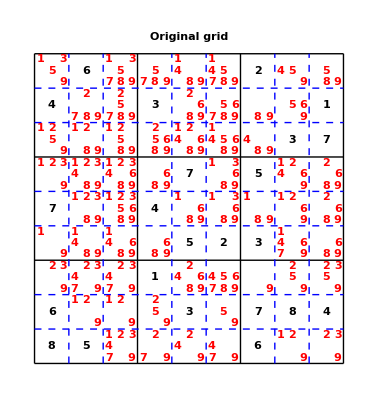

```mathematica
displaysys[systate,sysp,List@gridtitle["Original grid"]]
```